```mathematica
ClearAll["Global`*"];

Sol[Q_, L_, Nc_]:=Module[{},

(* ------------------------------------------------------- *)

(* verifica sulla dimensione del sistema *)
check0 = Length[Q]==Length[L] && Length[Q]==Nc && Length[L]==Nc;
If[check0==True,
Print["Le dimensioni degli elementi sono compatibili"],
Print[Style["Le dimensioni degli elementi non sono compatibili. Ricontrollare", FontColor->Red]]
];

(* vettore dei momenti incogniti (positivi per fibre tese all'intradosso) *)
M=Array[m, Nc+1]; 

(* SOLUZIONE DEL SISTEMA LINEARE *)

{R, K} = CoefficientArrays[
Append[
Append[
Table[
M[[i]]*L[[i]]/(6*EJ)+M[[i+1]]*L[[i]]/(3*EJ)+Q[[i]]*L[[i]]^3/(24*EJ)+M[[i+1]]*L[[i+1]]/(3*EJ)+Q[[i+1]]*L[[i+1]]^3/(24*EJ)+M[[i+2]]*L[[i+1]]/(6*EJ)==0,
{i, 1, Nc-1}], M[[1]]==0],Last[M]==0],
Table[m[i], {i, 1, Nc+1}]]//Normal;
R = -R;
MatrixForm[K];
MatrixForm[R];
MatrixForm[M];

M = LinearSolve[K, R]//FullSimplify;
Print["M = ",MatrixForm[M]];

(*M = M/.Solve[M.K-R==0, M][[1]];*)


(* Reazioni vincolari (positive verso l'alto) *)

V = Array[v, Nc+1];
{RV, MV} = CoefficientArrays[
 Append[
Prepend[
Table[V[[i]]==(M[[i-1]]-M[[i]])/L[[i-1]]-(M[[i]]-M[[i+1]])/L[[i]]+1/2*(Q[[i-1]]*L[[i-1]]+Q[[i]]*L[[i]]), {i, 2, Nc}
],
Table[V[[j]]==1/2*Q[[j]]*L[[j]]-(M[[j]]-M[[j+1]])/L[[j]], {j, 1,1}][[1]]
],
Table[V[[j]]==1/2*Q[[j]]*L[[j]]+(M[[j]]-M[[j+1]])/L[[j]], {j, Nc,Nc}][[1]]
],
Table[V[[i]], {i, 1, Nc+1}]
]//Normal//Simplify;
RV = -RV;
Print["R_V = ", MatrixForm[RV]];


(* verifica equilibrio alla traslazione verticale *)

check = Sum[RV[[i]], {i, 1, Length[RV]}]-Sum[Q[[i]]*L[[i]], {i, 1, Length[Q]}]//FullSimplify;
If[check == 0, 
Print[Style["Equilibrio alla traslazione verticale soddisfatto", FontColor->Automatic]], 
Print[Style["Equilibrio alla traslazione verticale soddisfatto", FontColor->Red]]]

]
```

```mathematica
(* numero di campate. Inserire il valore numerico *)
Nc = 10;

(* vettore dei carichi trasversali distribuiti. Inserire il valore numerico *)
Q0 = {1,0,0,0,0,0,0,0,0,0};
Q= {5,5,5,5,5,5,5,5,5,5};
(* vettore delle lunghezze delle campate. Inserire il valore numerico *)
L= {5,5,5,5,5,5,5,5,5,5};

Sol[Q0,L,Nc]
```

Le dimensioni degli elementi sono compatibili

M = (0
-1013625/605264
16975/37829
-72775/605264
4875/151316
-25/2896
175/75658
-375/605264
25/151316
-25/605264
0)

R_V = (1310435/605264
986465/302632
-20370/37829
43665/302632
-2925/75658
15/1448
-105/37829
225/302632
-15/75658
15/302632
-5/605264)

Equilibrio alla traslazione verticale soddisfatto

```mathematica
M//N//MatrixForm
```

(0.
-1.67468
0.44873
-0.120237
0.0322173
-0.0086326
0.00231304
-0.000619564
0.000165217
-0.0000413043
0.)

```mathematica
L0= Append[L*0,0];
For[i=2, i<Nc+2, i++,
L0[[i]]= L0[[i-1]]+L[[i-1]];
]
L0
Ltot = Last[L0];
```

{0,5,10,15,20,25,30,35,40,45,50}

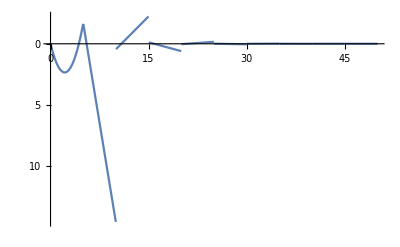

```mathematica
Plot[
Sum[(M[[i]]+RV[[i]]*(s-L0[[i]])-Q0[[i]]*(s-L0[[i]])^2/2)*(HeavisideTheta[s-L0[[i]]]-HeavisideTheta[s-L0[[i+1]]]),
{i, 1, Nc}],
{s, L0[[1]], Last[L0]},
ScalingFunctions->"Reverse",
PlotRange->Full
]
```

```mathematica
Ms1[s_]:= Evaluate[Sum[(M[[i]]+RV[[i]]*(s-L0[[i]])-Q0[[i]]*(s-L0[[i]])^2/2)*(HeavisideTheta[s-L0[[i]]]-HeavisideTheta[s-L0[[i+1]]]),
{i, 1, Nc}]];
Ms1[s]
```

(-25/605264+(15 (-45+s))/302632) (-HeavisideTheta[-50+s]+HeavisideTheta[-45+s])+(25/151316-(15 (-40+s))/75658) (-HeavisideTheta[-45+s]+HeavisideTheta[-40+s])+(-375/605264+(225 (-35+s))/302632) (-HeavisideTheta[-40+s]+HeavisideTheta[-35+s])+(175/75658-(105 (-30+s))/37829) (-HeavisideTheta[-35+s]+HeavisideTheta[-30+s])+(-25/2896+(15 (-25+s))/1448) (-HeavisideTheta[-30+s]+HeavisideTheta[-25+s])+(4875/151316-(2925 (-20+s))/75658) (-HeavisideTheta[-25+s]+HeavisideTheta[-20+s])+(-72775/605264+(43665 (-15+s))/302632) (-HeavisideTheta[-20+s]+HeavisideTheta[-15+s])+(16975/37829-(20370 (-10+s))/37829) (-HeavisideTheta[-15+s]+HeavisideTheta[-10+s])+(-1013625/605264+(986465 (-5+s))/302632) (-HeavisideTheta[-10+s]+HeavisideTheta[-5+s])+((1310435 s)/605264-s^2/2) (-HeavisideTheta[-5+s]+HeavisideTheta[s])

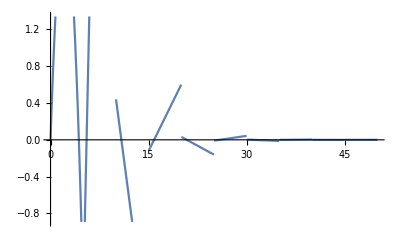

```mathematica
Plot[Ms1[s], {s, 0, Ltot}]
```

```mathematica
M1=(X1[0]+R1[0]*s-s**2/2)*(Hv(s)-Hv(s-3))+(X1[1]+R1[1]*(s-3))*(Hv(s-3)-Hv(s-(3+4.5)))+(X1[2]+R1[2]*(s-(3+4.5)))*(Hv(s-(3+4.5))-Hv(s-(3+4.5+4)))+(X1[3]+R1[3]*(s-(3+4.5+4)))*(Hv(s-(3+4.5+4))-Hv(s-(3+4.5+4+5)))+(X1[4]+R1[4]*(s-(3+4.5+4+5)))*(Hv(s-(3+4.5+4+5))-Hv(s-(3+4.5+4+5+6.15)))+(X1[5]+R1[5]*(s-(3+4.5+4+5+6.15)))*(Hv(s-(3+4.5+4+5+6.15))-Hv(s-(3+4.5+4+5+6.15+4)))
```